```mathematica
Sx=(1/Sqrt[2]) {{0,1,0},{1,0,1},{0,1,0}};
Sy=(I/Sqrt[2]) {{0,-1,0},{1,0,-1},{0,1,0}};
Sz={{1,0,0},{0,0,0},{0,0,-1}};
```

```mathematica
indent3 = IdentityMatrix[3];
```

```mathematica
num = {gamma-> 0.3077*10^-3,elektrona->  2.803, apar ->  -2.7, aper-> -1.14};
numfull = {gamma-> 0.3077*10^-3,elektrona->  2.803, apar ->  -2.7, aper-> -1.14, d-> 2875, Mz-> 10, Bx -> 10, By -> 10,Bz -> 10, Mx-> 4, My-> 3, Ny-> 4,Nx-> 4};
```

```mathematica
numbezD = {gamma-> 0.3077*10^-3,elektrona->  2.803, apar ->  -2.7, aper-> -1.14, Mz-> 10, Bx -> 10, By -> 10,Bz -> 10, Mx-> 4, My-> 3, Ny-> 4,Nx-> 4};
ddd= {2860,2880}
```

{2860,2880}

```mathematica
numbezB = {gamma-> 0.3077*10^-3,elektrona->  2.803, apar ->  -2.7, aper-> -1.14, Mz-> 10, Mx-> 4, My-> 3, Ny-> 4,Nx-> 4,d-> 2075};
ddd= {2860,2880}
numbezBz = {gamma-> 0.3077*10^-3,elektrona->  2.803, apar ->  -2.7, aper-> -1.14, Mz-> 10, Mx-> 4, My-> 3, Ny-> 4,Nx-> 4,d-> 2075, Bx -> 10, By -> 10};
```

{2860,2880}

```mathematica
Hel=elektrona*(Bx*Sx+By*Sy+Bz*Sz);

HZFS=d*Sz.Sz-((2*indent3)/3);

Hstrain=Mz*(Sz.Sz)+Mx*(Sx.Sx-Sy.Sy)+My*(Sx.Sy+Sy.Sx)+Nx*(Sz.Sx+Sx.Sz)+Ny*(Sy.Sz+Sz.Sy);
```

```mathematica
(Htot = Hel+HZFS+Hstrain)//MatrixForm
```

(-2/3+d+Bz elektrona+Mz | (Bx/(√2)-(ⅈ By)/(√2)) elektrona+Nx/(√2)-(ⅈ Ny)/(√2) | Mx-ⅈ My
(Bx/(√2)+(ⅈ By)/(√2)) elektrona+Nx/(√2)+(ⅈ Ny)/(√2) | -2/3 | (Bx/(√2)-(ⅈ By)/(√2)) elektrona-Nx/(√2)+(ⅈ Ny)/(√2)
Mx+ⅈ My | (Bx/(√2)+(ⅈ By)/(√2)) elektrona-Nx/(√2)-(ⅈ Ny)/(√2) | -2/3+d-Bz elektrona+Mz)

```mathematica
eigen = Eigenvalues[Htot]  //ToRadicals;
```

```mathematica
SetPrecision[eigen/.numfull,20]
```

{2913.1856484435361381-2.5769×10^-12 ⅈ,-1.2203075385764350358,2856.034659095040297+2.7285×10^-12 ⅈ}

```mathematica
en1 =eigen[[1]]-eigen[[2]];
```

```mathematica
en2 = eigen[[3]]-eigen[[2]];
```

```mathematica
starp = en1-en2//Simplify
```

(6 d^2-2 ⅈ √3 d^2+18 Bx^2 elektrona^2-6 ⅈ √3 Bx^2 elektrona^2+18 By^2 elektrona^2-6 ⅈ √3 By^2 elektrona^2+18 Bz^2 elektrona^2-6 ⅈ √3 Bz^2 elektrona^2+18 Mx^2-6 ⅈ √3 Mx^2+18 My^2-6 ⅈ √3 My^2+12 d Mz-4 ⅈ √3 d Mz+6 Mz^2-2 ⅈ √3 Mz^2+18 Nx^2-6 ⅈ √3 Nx^2+18 Ny^2-6 ⅈ √3 Ny^2+3 2^(1/3) (-2 d^3-9 Bx^2 d elektrona^2-9 By^2 d elektrona^2+18 Bz^2 d elektrona^2+27 Bx^2 elektrona^2 Mx-27 By^2 elektrona^2 Mx+18 d Mx^2+54 Bx By elektrona^2 My+18 d My^2-6 d^2 Mz-9 Bx^2 elektrona^2 Mz-9 By^2 elektrona^2 Mz+18 Bz^2 elektrona^2 Mz+18 Mx^2 Mz+18 My^2 Mz-6 d Mz^2-2 Mz^3+54 Bx Bz elektrona^2 Nx-9 d Nx^2-27 Mx Nx^2-9 Mz Nx^2+54 By Bz elektrona^2 Ny-54 My Nx Ny-9 d Ny^2+27 Mx Ny^2-9 Mz Ny^2+√(-4 (d^2+3 Bx^2 elektrona^2+3 By^2 elektrona^2+3 Bz^2 elektrona^2+3 Mx^2+3 My^2+2 d Mz+Mz^2+3 Nx^2+3 Ny^2)^3+(2 d^3+27 By^2 elektrona^2 Mx+6 d^2 Mz+9 By^2 elektrona^2 Mz-18 Bz^2 elektrona^2 Mz-18 Mx^2 Mz-18 My^2 Mz+2 Mz^3+9 Bx^2 elektrona^2 (-3 Mx+Mz)+27 Mx Nx^2+9 Mz Nx^2-54 Bx elektrona^2 (By My+Bz Nx)-54 By Bz elektrona^2 Ny+54 My Nx Ny-27 Mx Ny^2+9 Mz Ny^2+3 d (3 Bx^2 elektrona^2+3 By^2 elektrona^2-6 Bz^2 elektrona^2-6 Mx^2-6 My^2+2 Mz^2+3 Nx^2+3 Ny^2))^2))^(2/3)+ⅈ 2^(1/3) √3 (-2 d^3-9 Bx^2 d elektrona^2-9 By^2 d elektrona^2+18 Bz^2 d elektrona^2+27 Bx^2 elektrona^2 Mx-27 By^2 elektrona^2 Mx+18 d Mx^2+54 Bx By elektrona^2 My+18 d My^2-6 d^2 Mz-9 Bx^2 elektrona^2 Mz-9 By^2 elektrona^2 Mz+18 Bz^2 elektrona^2 Mz+18 Mx^2 Mz+18 My^2 Mz-6 d Mz^2-2 Mz^3+54 Bx Bz elektrona^2 Nx-9 d Nx^2-27 Mx Nx^2-9 Mz Nx^2+54 By Bz elektrona^2 Ny-54 My Nx Ny-9 d Ny^2+27 Mx Ny^2-9 Mz Ny^2+√(-4 (d^2+3 Bx^2 elektrona^2+3 By^2 elektrona^2+3 Bz^2 elektrona^2+3 Mx^2+3 My^2+2 d Mz+Mz^2+3 Nx^2+3 Ny^2)^3+(2 d^3+27 By^2 elektrona^2 Mx+6 d^2 Mz+9 By^2 elektrona^2 Mz-18 Bz^2 elektrona^2 Mz-18 Mx^2 Mz-18 My^2 Mz+2 Mz^3+9 Bx^2 elektrona^2 (-3 Mx+Mz)+27 Mx Nx^2+9 Mz Nx^2-54 Bx elektrona^2 (By My+Bz Nx)-54 By Bz elektrona^2 Ny+54 My Nx Ny-27 Mx Ny^2+9 Mz Ny^2+3 d (3 Bx^2 elektrona^2+3 By^2 elektrona^2-6 Bz^2 elektrona^2-6 Mx^2-6 My^2+2 Mz^2+3 Nx^2+3 Ny^2))^2))^(2/3))/(6 2^(2/3) (-2 d^3-9 Bx^2 d elektrona^2-9 By^2 d elektrona^2+18 Bz^2 d elektrona^2+27 Bx^2 elektrona^2 Mx-27 By^2 elektrona^2 Mx+18 d Mx^2+54 Bx By elektrona^2 My+18 d My^2-6 d^2 Mz-9 Bx^2 elektrona^2 Mz-9 By^2 elektrona^2 Mz+18 Bz^2 elektrona^2 Mz+18 Mx^2 Mz+18 My^2 Mz-6 d Mz^2-2 Mz^3+54 Bx Bz elektrona^2 Nx-9 d Nx^2-27 Mx Nx^2-9 Mz Nx^2+54 By Bz elektrona^2 Ny-54 My Nx Ny-9 d Ny^2+27 Mx Ny^2-9 Mz Ny^2+√(-4 (d^2+3 Bx^2 elektrona^2+3 By^2 elektrona^2+3 Bz^2 elektrona^2+3 Mx^2+3 My^2+2 d Mz+Mz^2+3 Nx^2+3 Ny^2)^3+(2 d^3+27 By^2 elektrona^2 Mx+6 d^2 Mz+9 By^2 elektrona^2 Mz-18 Bz^2 elektrona^2 Mz-18 Mx^2 Mz-18 My^2 Mz+2 Mz^3+9 Bx^2 elektrona^2 (-3 Mx+Mz)+27 Mx Nx^2+9 Mz Nx^2-54 Bx elektrona^2 (By My+Bz Nx)-54 By Bz elektrona^2 Ny+54 My Nx Ny-27 Mx Ny^2+9 Mz Ny^2+3 d (3 Bx^2 elektrona^2+3 By^2 elektrona^2-6 Bz^2 elektrona^2-6 Mx^2-6 My^2+2 Mz^2+3 Nx^2+3 Ny^2))^2))^(1/3))

```mathematica
staaa=starp /.numbezBz // Simplify
```

((2.74166×10^6-1.5829×10^6 ⅈ)+(14.8484-8.57275 ⅈ) Bz^2+(0.39685+0.229122 ⅈ) (-1.8157×10^10+33941.4 Bz+294866. Bz^2+√(-5.59492×10^16-1.23255×10^15 Bz-1.60651×10^16 Bz^2+2.00163×10^10 Bz^3+5.79314×10^10 Bz^4-52379.6 Bz^6))^(2/3))/(-1.8157×10^10+33941.4 Bz+294866. Bz^2+√(-5.59492×10^16-1.23255×10^15 Bz-1.60651×10^16 Bz^2+2.00163×10^10 Bz^3+5.79314×10^10 Bz^4-52379.6 Bz^6))^(1/3)

```mathematica
{staaa/. Bz-> 1, staaa/. Bz-> 1.01}
```

{11.9681+6.86562×10^-13 ⅈ,11.9954-2.15028×10^-12 ⅈ}

```mathematica
starp /.numbezD //Simplify
```

((4625.25-2670.39 ⅈ)+(12.5992-7.27416 ⅈ) d+(0.629961-0.363708 ⅈ) d^2+(0.39685+0.229122 ⅈ) (463722.-438. d-60. d^2-2. d^3+√(-1.36813×10^12-1.33439×10^10 d-7.37579×10^8 d^2-5.35855×10^6 d^3-87553.5 d^4))^(2/3))/(463722.-438. d-60. d^2-2. d^3+√(-1.36813×10^12-1.33439×10^10 d-7.37579×10^8 d^2-5.35855×10^6 d^3-87553.5 d^4))^(1/3)

```mathematica
starpbezd = starp /.numbezD
```

((44052.8-25433.9 ⅈ)+120 d-40 ⅈ √3 d+6 d^2-2 ⅈ √3 d^2+3 2^(1/3) (463722.-438. d-60 d^2-2 d^3+√(-4 (7342.13+20 d+d^2)^3+(-463722.+438. d+60 d^2+2 d^3)^2))^(2/3)+ⅈ 2^(1/3) √3 (463722.-438. d-60 d^2-2 d^3+√(-4 (7342.13+20 d+d^2)^3+(-463722.+438. d+60 d^2+2 d^3)^2))^(2/3))/(6 2^(2/3) (463722.-438. d-60 d^2-2 d^3+√(-4 (7342.13+20 d+d^2)^3+(-463722.+438. d+60 d^2+2 d^3)^2))^(1/3))

```mathematica
dddddd=Re[starpbezd]/.d->#&/@ddd//N
```

{57.152,57.1506}

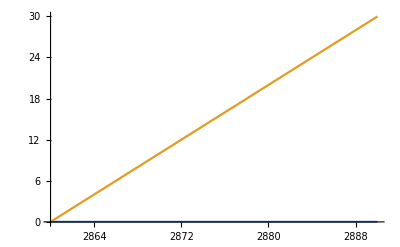

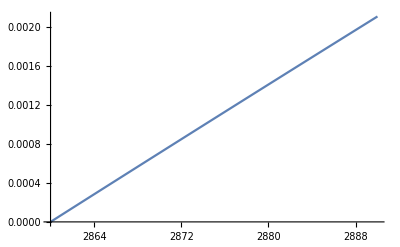

-5.32794×10^-6

-0.0749756

```mathematica
starp1=Re[starpbezd]/. d-> 2860;
starp1deg= Re[starpbezd]/. d-> 2860.075;
en11=Re[en1 /.numbezD ]/.d-> 2860;
en11deg=Re[en1 /.numbezD ]/.d-> 2860.075;
Plot[{Re[starpbezd]-starp1,Re[en1 /.numbezD ]-en11},{d,2860,2890}]
Plot[{starp1-Re[starpbezd /.numbezD ]},{d,2860,2890}]
starpuzdeg = starp1deg-starp1
en1uzdeg=en11-en11deg
```

```mathematica
en1uzdeg/starpuzdeg
```

14072.2

```mathematica
57.1520495123101
```

57.152

```mathematica
ee =SetPrecision[en1 /.numbezD //Simplify,20]
```

((27751.505232643939962+16022.3390164842931 ⅈ)+(75.595262993692386999+43.64494543886884514 ⅈ) d+(3.77976314968461935+2.182247271943442257 ⅈ) d^2+(0.066141710498674968766-0.03818693436107228889 ⅈ) (1.0016405019359999895×10^8-94608. d-12960. d^2-432. d^3+√(-6.3831255490173264×10^16-6.225713038104055×10^14 d-3.4412495429244050781×10^13 d^2-2.5000856975139837646×10^11 d^3-4.0848978316031990051×10^9 d^4))^(2/3))/(1.0016405019359999895×10^8-94608. d-12960. d^2-432. d^3+√(-6.3831255490173264×10^16-6.225713038104055×10^14 d-3.4412495429244050781×10^13 d^2-2.5000856975139837646×10^11 d^3-4.0848978316031990051×10^9 d^4))^(1/3)

```mathematica
eeeeee= SetPrecision[ee/.d->#&/@ddd//N,20]
```

{2899.4108093662694046-1.64×10^-13 ⅈ,2919.4043493236963513-1.65×10^-13 ⅈ}

```mathematica
je = (eeeeee[[2]]-eeeeee[[1]])
```

19.993539957426947-1.×10^-15 ⅈ

```mathematica
ej=dddddd[[2]]-dddddd[[1]]
```

-0.00141115

```mathematica
je/ej
```

-14168.3+8.13129×10^-13 ⅈ

```mathematica
sarpB=starp /. numbezB
```

(26084376-8694792 ⅈ √3+(141.423-81.6504 ⅈ) Bx^2+(141.423-81.6504 ⅈ) By^2+(141.423-81.6504 ⅈ) Bz^2+3 2^(1/3) (-18127593072-146584. Bx^2+1272.8 Bx By-148282. By^2+1697.07 Bx Bz+1697.07 By Bz+294866. Bz^2+√(-4 (4347396+23.5704 Bx^2+23.5704 By^2+23.5704 Bz^2)^3+(18126684222-141.423 Bx^2+1555.65 By^2-1697.07 By Bz-1414.23 Bz^2-424.268 Bx (3 By+4 Bz)+6225 (146+23.5704 Bx^2+23.5704 By^2-47.1409 Bz^2))^2))^(2/3)+ⅈ 2^(1/3) √3 (-18127593072-146584. Bx^2+1272.8 Bx By-148282. By^2+1697.07 Bx Bz+1697.07 By Bz+294866. Bz^2+√(-4 (4347396+23.5704 Bx^2+23.5704 By^2+23.5704 Bz^2)^3+(18126684222-141.423 Bx^2+1555.65 By^2-1697.07 By Bz-1414.23 Bz^2-424.268 Bx (3 By+4 Bz)+6225 (146+23.5704 Bx^2+23.5704 By^2-47.1409 Bz^2))^2))^(2/3))/(6 2^(2/3) (-18127593072-146584. Bx^2+1272.8 Bx By-148282. By^2+1697.07 Bx Bz+1697.07 By Bz+294866. Bz^2+√(-4 (4347396+23.5704 Bx^2+23.5704 By^2+23.5704 Bz^2)^3+(18126684222-141.423 Bx^2+1555.65 By^2-1697.07 By Bz-1414.23 Bz^2-424.268 Bx (3 By+4 Bz)+6225 (146+23.5704 Bx^2+23.5704 By^2-47.1409 Bz^2))^2))^(1/3))

```mathematica
nvcentri={{-1,-1,1},{1,1,1},{-1,1,-1},{1,-1,-1}}/Sqrt[3];
```

```mathematica
BmagValues=Range[0,10,50];(*magnetic field range*)
```

```mathematica
sarpBFunc[Bx_,By_,Bz_]:=((26084376-8694792 ⅈ √3+(141.422562-81.65035424018653 ⅈ) Bx^2+(141.422562-81.65035424018653 ⅈ) By^2+(141.422562-81.65035424018653 ⅈ) Bz^2+3 2^(1/3) (-18127593072-146584.48551299996 Bx^2+1272.803058 Bx By-148281.556257 By^2+1697.0707439999999 Bx Bz+1697.0707439999999 By Bz+294866.04176999995 Bz^2+√(-4 (4347396+23.570427 Bx^2+23.570427 By^2+23.570427 Bz^2)^3+(18126684222-141.422562 Bx^2+1555.648182 By^2-1697.0707439999999 By Bz-1414.22562 Bz^2-424.26768599999997 Bx (3 By+4 Bz)+6225 (146+23.570427 Bx^2+23.570427 By^2-47.140854 Bz^2))^2))^(2/3)+ⅈ 2^(1/3) √3 (-18127593072-146584.48551299996 Bx^2+1272.803058 Bx By-148281.556257 By^2+1697.0707439999999 Bx Bz+1697.0707439999999 By Bz+294866.04176999995 Bz^2+√(-4 (4347396+23.570427 Bx^2+23.570427 By^2+23.570427 Bz^2)^3+(18126684222-141.422562 Bx^2+1555.648182 By^2-1697.0707439999999 By Bz-1414.22562 Bz^2-424.26768599999997 Bx (3 By+4 Bz)+6225 (146+23.570427 Bx^2+23.570427 By^2-47.140854 Bz^2))^2))^(2/3))/(6 2^(2/3) (-18127593072-146584.48551299996 Bx^2+1272.803058 Bx By-148281.556257 By^2+1697.0707439999999 Bx Bz+1697.0707439999999 By Bz+294866.04176999995 Bz^2+√(-4 (4347396+23.570427 Bx^2+23.570427 By^2+23.570427 Bz^2)^3+(18126684222-141.422562 Bx^2+1555.648182 By^2-1697.0707439999999 By Bz-1414.22562 Bz^2-424.26768599999997 Bx (3 By+4 Bz)+6225 (146+23.570427 Bx^2+23.570427 By^2-47.140854 Bz^2))^2))^(1/3)))
```